# Coupled Isodesmic Model

## Supporting Information Insights into chemically-fueled supramolecular polymers

Anastasiia Sharko, Dimitri Livitz, Serena De Piccoli1, Kyle J. M. Bishop, and Thomas M. Hermans

```mathematica
ClearAll[MPLColorMap]
<<"http://pastebin.com/raw/pFsb4ZBS";
bigSize = 14;
smallSize=12;
thin =0.6;
```

## Numerical Solution

### Moment evolution equations (4.4)

UNITS: Concentrations scaled by c_tot and time by (k_a c_tot)^-1

```mathematica
tmax = 5; (* maximum time *)
kd1=1; (* rate constant for deactivation, Subscript[k, d1]' *) 
kd2=10; (* rate constant for deactivation, Subscript[k, d2]' *) 
f0=1;  (* initial activating fuel concentration, Subscript[f, 0] *) 
kn=1; (* rate constant for disassembly, k_- *) 
L=5; (* average length at equilibrium if all monomer were activated *)
kp=kn L(L-1);(* rate constant for assembly *)
```

Integrate numerically.  Note that deactivated monomer concentration is d(t)=1-a_1-m'_1 and g=constant.

```mathematica
solm=NDSolve[{
f'[t]==-f[t](1-a1[t]-m1p[t]),
a1'[t]==f[t](1-a1[t]-m1p[t])-kd1 a1[t]+2kd2 m0p[t]-2 kp a1[t](a1[t]+m0p[t])+2 kn m0p[t],
m0p'[t]==kd2 (m1p[t]-4m0p[t])+kp(a1[t]^2-m0p[t]^2)+kn(m1p[t]-3m0p[t]),
m1p'[t]==-kd2 (m1p[t]+2m0p[t]
)+2 kp a1[t](a1[t]+m0p[t])-2 kn m0p[t],
f[0]==f0,
a1[0]==0,
m0p[0]==0,
m1p[0]==0},{f[t],a1[t],m0p[t],m1p[t]},{t,0,tmax}];
```

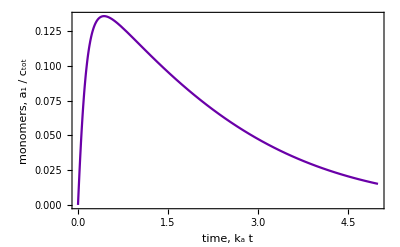

```mathematica
Plot[{a1[t]/.solm[[1]]},{t,0,tmax},
Frame->True,
PlotRange->Full,
PlotStyle->{MPLColorMap["Plasma"][0.2]},
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time, k_a t"],Style["monomers, a_1 / c_tot"]}]
```

### Polymer distribution evolution equations (4.1)

Specify parameters

```mathematica
nmax=100; (* maximum polymer size *)
```

Integrate numerically.

```mathematica
Clear[a]
nn =Table[n,{n,1,nmax}];
aa[t_]=Table[Subscript[a, n][t],{n,1,nmax}];
aa0=Table[0,{n,1,nmax}];

(* governing equations *)
rhs=Table[
KroneckerDelta[1,n](f[t](1-Sum[j Subscript[a, j][t],{j,1,nmax}])-kd1 Subscript[a, 1][t]+kd2 Subscript[a, 1][t])
-kd2 n Subscript[a, n][t]
+2 kd2 Sum[Subscript[a, j+n][t],{j,1,nmax-n}]
-2 kp Subscript[a, n][t] Sum[Subscript[a, j][t],{j,1,nmax}]
+ kp  Sum[Subscript[a, j][t]Subscript[a, n-j][t],{j,1,n-1}]
-kn(n-1)Subscript[a, n][t]
+2kn Sum[Subscript[a, n+j][t],{j,1,nmax-n}],
{n,1,nmax}];
eqns=Flatten[{
f'[t]==-f[t](1-Sum[j Subscript[a, j][t],{j,1,nmax}]),
Thread[D[aa[t],t]==rhs]}];
(* initial conditions *)
initc=Flatten[{f[0]==f0,Thread[aa[0]==aa0]}];
(* solution *)
sol=NDSolve[{eqns,initc},aa[t],{t,0,tmax}];
```

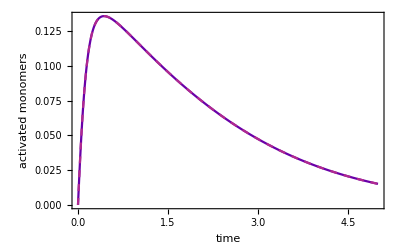

```mathematica
Plot[{Subscript[a, 1][t]/.sol[[1]],a1[t]/.solm[[1]]},{t,0,tmax},
Frame->True,
PlotRange->Full,
PlotStyle->{MPLColorMap["Plasma"][0.2],Directive[Dashed,MPLColorMap["Plasma"][0.4]]},
LabelStyle->{FontSize->12,Black},
FrameLabel->{Style["time"],Style["activated monomers"]}]
```

## Example I: Polymers Inhibit Deactivation (k_d2=0)

### Regime III: f_0≪k'_d and k'_d≫1 UNCOUPLED

```mathematica
kd=20;
f0=1;
tmax=30;
```

```mathematica
Clear[m1,f,t];
sol=NDSolve[{
f'[t]==- f[t] (1-m1[t]),
m1'[t]== f[t] (1-m1[t])-kd m1[t],
m1[0]==0,
f[0]==f0},{f[t],m1[t]},{t,0,tmax}];
```

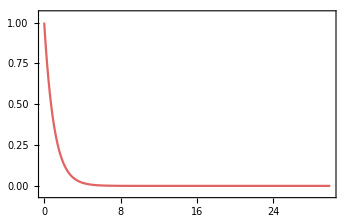
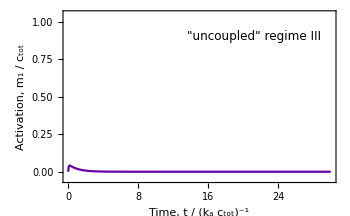

```mathematica
plot1=Plot[{m1[t]/.sol[[1]]},{t,0,tmax},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{
Style["Time, t / (k_a c_tot)^-1 ",FontSize->bigSize],
Style["Activation, m_1 / c_tot",FontSize->bigSize]},
PlotRange->{-0.05,1.05}f0,
PlotStyle->{Directive[MPLColorMap["Plasma"][0.2]]},
ImageSize->350,
ImagePadding->{{50,50},{50,25}},
Frame->{True,True,True,False},
FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]]},
Epilog->{Text[Style["\"uncoupled\" regime III",smallSize],Scaled[{0.7,0.85}]]}];
plot2=Plot[{f[t]/.sol[[1]]},{t,0,tmax},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.6]]},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{{None,Rotate[Style["Fuel, f / c_tot",FontSize->bigSize],180 Degree]},{None,None}},
PlotRange->{-0.05,1.05}f0,
ImageSize->350,
ImagePadding->{{50,50},{50,25}},
Axes->False,
Frame->{False,False,False,True},
FrameTicks->{{None,All},{None,None}},FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.6],AbsoluteThickness[thin]]}];

uncoupled=Overlay[{plot2,plot1}]
```

### Regime III: f_0≪k'_d and k'_d≫1 COUPLED

```mathematica
kd1=20; (* rate constant for deactivation *) 
kd2=0; (* rate constant for deactivation *) 
kp=400 √5; (* rate for assembly *)
kn=kp/400 ;(* rate constant for disassembly *)
```

```mathematica
solm=NDSolve[{
f'[t]==-f[t](1-a1[t]-m1p[t]),
a1'[t]==f[t](1-a1[t]-m1p[t])-kd1 a1[t]+2kd2 m0p[t]-2 kp a1[t](a1[t]+m0p[t])+2 kn m0p[t],
m0p'[t]==kd2 (m1p[t]-4m0p[t])+kp(a1[t]^2-m0p[t]^2)+kn(m1p[t]-3m0p[t]),
m1p'[t]==-kd2 (m1p[t]+2m0p[t])+2 kp a1[t](a1[t]+m0p[t])-2 kn m0p[t],
f[0]==f0,
a1[0]==0,
m0p[0]==0,
m1p[0]==0},{f[t],a1[t],m0p[t],m1p[t]},{t,0,tmax}];
```

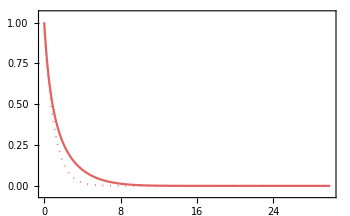
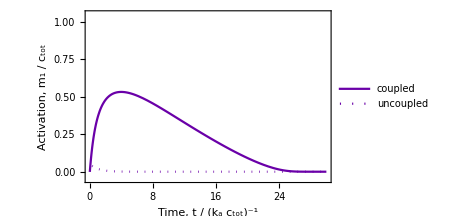

```mathematica
plot1=Plot[{a1[t]+m1p[t]/.solm[[1]],m1[t]/.sol[[1]]},{t,0,tmax},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{
Style["Time, t / (k_a c_tot)^-1 ",FontSize->bigSize],
Style["Activation, m_1 / c_tot",FontSize->bigSize]},
PlotRange->{-0.05,1.05}f0,
PlotStyle->{Directive[MPLColorMap["Plasma"][0.2]],Directive[MPLColorMap["Plasma"][0.2],Dotted]},
ImageSize->350,
ImagePadding->{{50,50},{50,25}},
Frame->{True,True,True,False},
PlotLegends->Placed[{Style["coupled",FontSize->smallSize],
Style["uncoupled",FontSize->smallSize]},Scaled[{0.75,0.8}]],
FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]]}];
plot2=Plot[{f[t]/.solm[[1]],f[t]/.sol[[1]]},{t,0,tmax},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.6]],Directive[MPLColorMap["Plasma"][0.6],Dotted]},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{{None,Rotate[Style["Fuel, f / c_tot",FontSize->bigSize],180 Degree]},{None,None}},
PlotRange->{-0.05,1.05}f0,
ImageSize->350,
ImagePadding->{{50,50},{50,25}},
Axes->False,
Frame->{False,False,False,True},
FrameTicks->{{None,All},{None,None}},FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.6],AbsoluteThickness[thin]]}];

coupled=Overlay[{plot2,plot1}]
```

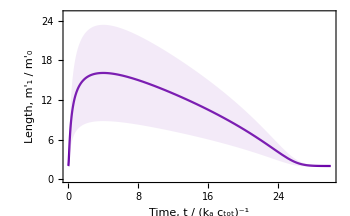

```mathematica
dpPlot=Show[
Plot[{m1p[t]/m0p[t]/.solm[[1]]},{t,0,30},
Frame->True,
PlotRange->{0,25},
PlotStyle->{MPLColorMap["Plasma"][0.2]},
LabelStyle->{FontSize->12,Black},
ImageSize->350,
ImagePadding->{{50,50},{50,25}},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{
Style["Time, t / (k_a c_tot)^-1",FontSize->bigSize],
Style["Length, m'_1 / m'_0",FontSize->bigSize]}],
Plot[{m1p[t]/m0p[t]-0.5Sqrt[2+(m1p[t] (-3 m0p[t]+m1p[t]))/m0p[t]^2]/.solm[[1]],
m1p[t]/m0p[t]+0.5Sqrt[2+(m1p[t] (-3 m0p[t]+m1p[t]))/m0p[t]^2]/.solm[[1]]},{t,0,30},
Filling->{1->{2}},
PlotStyle->None,
FillingStyle->Directive[Lighter[MPLColorMap["Plasma"][0.2],0.6]]]]
```

#### Supplementary Figure 7

```mathematica
grid=Style[Grid[{{Graphics[{Inset[coupled],
Text[Style["a",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}}],
Graphics[{Inset[dpPlot],
Text[Style["b",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}}]}}],ImageSizeMultipliers->{1,1}]
```

-Graphics-

```mathematica
(* Export[NotebookDirectory[]<>"figures/coupled_plot_cataytic.pdf",grid]*)
```

## Example II: Polymers Enhance Deactivation (k_d1=0)

### Regime III: f_0≪k'_d and k'_d≫1 UNCOUPLED

```mathematica
kd=20;
f0=1;
tmax=30;
```

```mathematica
Clear[m1,f,t];
sol=NDSolve[{
f'[t]==- f[t] (1-m1[t]),
m1'[t]== f[t] (1-m1[t])-kd m1[t],
m1[0]==0,
f[0]==f0},{f[t],m1[t]},{t,0,tmax}];
```

```mathematica
plot1=Plot[{m1[t]/.sol[[1]]},{t,0,tmax},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{
Style["Time, t / (k_a c_tot)^-1 ",FontSize->bigSize],
Style["Activation, m_1 / c_tot",FontSize->bigSize]},
PlotRange->{-0.05,1.05}f0,
PlotStyle->{Directive[MPLColorMap["Plasma"][0.2]]},
ImageSize->350,
ImagePadding->{{50,50},{50,25}},
Frame->{True,True,True,False},
FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]]},
Epilog->{Text[Style["\"uncoupled\" regime III",smallSize],Scaled[{0.7,0.85}]]}];
plot2=Plot[{f[t]/.sol[[1]]},{t,0,tmax},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.6]]},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{{None,Rotate[Style["Fuel, f / c_tot",FontSize->bigSize],180 Degree]},{None,None}},
PlotRange->{-0.05,1.05}f0,
ImageSize->350,
ImagePadding->{{50,50},{50,25}},
Axes->False,
Frame->{False,False,False,True},
FrameTicks->{{None,All},{None,None}},FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.6],AbsoluteThickness[thin]]}];

uncoupled=Overlay[{plot2,plot1}]
```

-Graphics--Graphics-

### Regime III: f_0≪k'_d and k'_d≫1 COUPLED

```mathematica
kd1=0; (* rate constant for deactivation *) 
kd2=20; (* rate constant for deactivation *) 
kp=1; (* rate for assembly *)
kn=kp/400 ;(* rate constant for disassembly *)
```

```mathematica
solm=NDSolve[{
f'[t]==-f[t](1-a1[t]-m1p[t]),
a1'[t]==f[t](1-a1[t]-m1p[t])-kd1 a1[t]+2kd2 m0p[t]-2 kp a1[t](a1[t]+m0p[t])+2 kn m0p[t],
m0p'[t]==kd2 (m1p[t]-4m0p[t])+kp(a1[t]^2-m0p[t]^2)+kn(m1p[t]-3m0p[t]),
m1p'[t]==-kd2 (m1p[t]+2m0p[t])+2 kp a1[t](a1[t]+m0p[t])-2 kn m0p[t],
f[0]==f0,
a1[0]==0,
m0p[0]==0,
m1p[0]==0},{f[t],a1[t],m0p[t],m1p[t]},{t,0,tmax}];
```

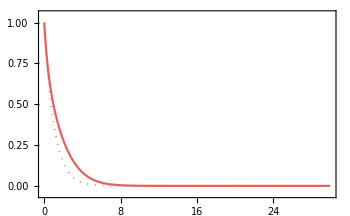
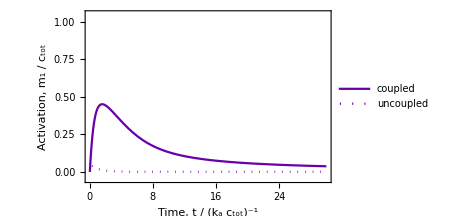

```mathematica
plot1=Plot[{a1[t]+m1p[t]/.solm[[1]],m1[t]/.sol[[1]]},{t,0,tmax},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{
Style["Time, t / (k_a c_tot)^-1 ",FontSize->bigSize],
Style["Activation, m_1 / c_tot",FontSize->bigSize]},
PlotRange->{-0.05,1.05}f0,
PlotStyle->{Directive[MPLColorMap["Plasma"][0.2]],Directive[MPLColorMap["Plasma"][0.2],Dotted]},
ImageSize->350,
ImagePadding->{{50,50},{50,25}},
Frame->{True,True,True,False},
PlotLegends->Placed[{Style["coupled",FontSize->smallSize],
Style["uncoupled",FontSize->smallSize]},Scaled[{0.75,0.8}]],
FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.2],AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]]}];
plot2=Plot[{f[t]/.solm[[1]],f[t]/.sol[[1]]},{t,0,tmax},
PlotStyle->{Directive[MPLColorMap["Plasma"][0.6]],Directive[MPLColorMap["Plasma"][0.6],Dotted]},
LabelStyle->Directive[Black,FontSize->smallSize],
FrameLabel->{{None,Rotate[Style["Fuel, f / c_tot",FontSize->bigSize],180 Degree]},{None,None}},
PlotRange->{-0.05,1.05}f0,
ImageSize->350,
ImagePadding->{{50,50},{50,25}},
Axes->False,
Frame->{False,False,False,True},
FrameTicks->{{None,All},{None,None}},FrameStyle->{
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[Black,AbsoluteThickness[thin]],
Directive[MPLColorMap["Plasma"][0.6],AbsoluteThickness[thin]]}];

coupled=Overlay[{plot2,plot1}]
```

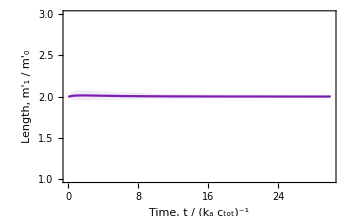

```mathematica
dpPlot=Show[
Plot[{m1p[t]/m0p[t]/.solm[[1]]},{t,0,30},
Frame->True,
PlotRange->{1,3},
PlotStyle->{MPLColorMap["Plasma"][0.2]},
LabelStyle->{FontSize->12,Black},
ImageSize->350,
ImagePadding->{{50,50},{50,25}},
FrameStyle->Directive[Black,AbsoluteThickness[thin]],
FrameLabel->{
Style["Time, t / (k_a c_tot)^-1",FontSize->bigSize],
Style["Length, m'_1 / m'_0",FontSize->bigSize]}],
Plot[{m1p[t]/m0p[t]-0.5Sqrt[2+(m1p[t] (-3 m0p[t]+m1p[t]))/m0p[t]^2]/.solm[[1]],
m1p[t]/m0p[t]+0.5Sqrt[2+(m1p[t] (-3 m0p[t]+m1p[t]))/m0p[t]^2]/.solm[[1]]},{t,0,30},
Filling->{1->{2}},
PlotStyle->None,
FillingStyle->Directive[Lighter[MPLColorMap["Plasma"][0.2],0.6]]]]
```

#### Supplementary Figure 8

```mathematica
grid=Style[Grid[{{Graphics[{Inset[coupled],
Text[Style["a",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}}],
Graphics[{Inset[dpPlot],
Text[Style["b",FontSize->bigSize],Scaled[{-0.18,1.04}]]},
ImageSize->350,
AspectRatio->1/GoldenRatio,
ImagePadding->{{50,50},{50,25}}]}}],ImageSizeMultipliers->{1,1}]
```

-Graphics-

```mathematica
(* Export[NotebookDirectory[]<>"figures/coupled_plot_cataytic.pdf",grid]*)
```